```mathematica
sqHeight = 90;
sqStd = 100;
minHeight = 60;
maxHeight = 200;
rk = 100;
SQ[z_] = PDF[NormalDistribution[sqHeight, sqStd], z] / PDF[NormalDistribution[sqHeight, sqStd], sqHeight];
R[z_, r_] = PDF[NormalDistribution[0, rk * r], z] / PDF[NormalDistribution[0, rk * r], minHeight];
Manipulate[Plot[{SQ[z]- R[z, r]},{z,minHeight,maxHeight}], {r, 0.01, 1}]
```

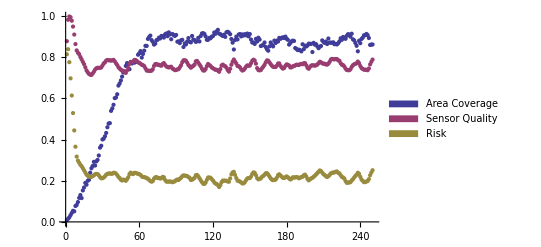

```mathematica
rdata = Import["~/Documents/Projects/rover/sandbox/all.txt", "Table"];
ListPlot[
Transpose[rdata][[{1,2,3}]],
PlotLegends-> SwatchLegend[{"Area Coverage", "Sensor Quality", "Risk"}]]
```